```mathematica
data={
{12,0.75,1.1499*10^10},
{9,0.4567,3.8453*10^9},
{15,1,7.8309*10^10},
{19,1.4485,6.2436*10^10}
};
line[n_,eps_]=Fit[data,{1,n,eps},{n,eps}]
epsilon[n_]=eps/.Solve[line[n,eps]==10^10,eps][[1]]//FullSimplify
```

-4.13366×10^11-8.15378×10^11 eps+8.70895×10^10 n

-0.519226+0.106809 n

```mathematica
epsilon[19]
```

1.51014

```mathematica
{6,0.5,3.411*10^4},
{6,0.75,618.6382},
{6,1,43.7257},
{6,0.25,3.4836*10^7},
{6,0.1,3.3310*10^11},
```

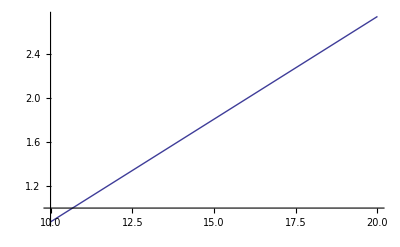

```mathematica
Plot[epsilon[n],{n,10,20}]
```